Pobranie danych z plików. Warto pomyśleć jak zapisane są pliki.

```mathematica
fn=FileNames["*.dat","C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\Frank-Hertz\\PG"];
TB=Import[#,"Table"]&/@ fn;
```

Wykresy danych pomiarowych:

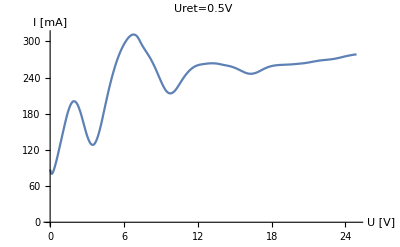
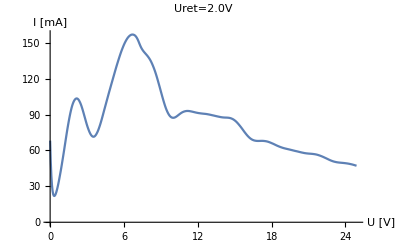
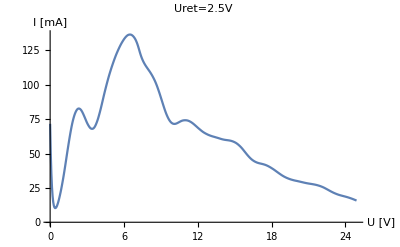
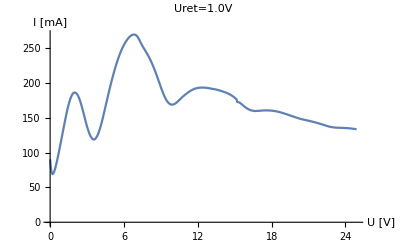
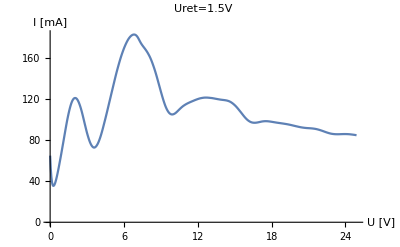
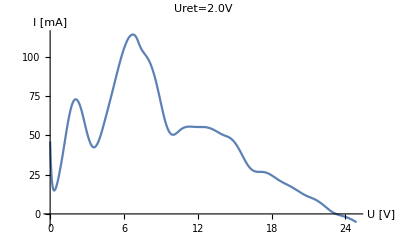
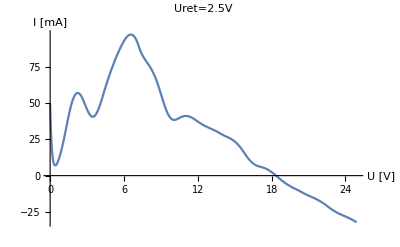
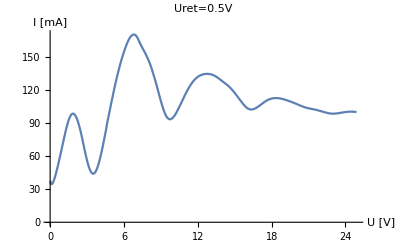

```mathematica
plots=ListLinePlot[#[[Range[2,Length[#]]]],AxesLabel->{"U [V]","I [mA]"},PlotLabel->ToString[#[[1]][[3]]]]&/@TB
```

Zapisywanie wykresów do pdf oddzielnie. Kolejność zależy od nazw plików z danymi.

```mathematica
For[i=1,i<=Length[plots],i++,Export["wyk"<>ToString[i]<>".pdf",plots[[i]]]]
```

Szukamy maksimum w przedziałach [0,4], [5,10] i [10,15]:

```mathematica
FindMaxUinInterval[Dane_,Int0_,IntF_]:=MaximalBy[Select[Dane[[2;;Length[Dane]]],#[[1]]≥Int0&&#[[1]]<=IntF&],Last]
UM1=First[First[FindMaxUinInterval[#,0,4]]]&/@TB
UM2=First[First[FindMaxUinInterval[#,5,10]]]&/@TB
UM3=First[First[FindMaxUinInterval[#,10,15]]]&/@TB
```

{1.95,2.15,2.35,2.,2.05,2.1,2.25,1.85,1.9,1.95,1.9,1.8,1.85,1.95,2.1,1.75,1.75,1.85,1.9,2.}

{6.8,6.7,6.5,6.8,6.8,6.7,6.55,6.8,6.85,6.8,6.8,6.8,6.85,6.75,6.65,6.8,6.85,6.8,6.75,6.7}

{13.2,11.15,10.95,12.35,12.7,11.35,11.05,12.75,12.7,12.7,12.75,12.8,12.65,12.6,11.2,12.8,12.8,12.7,12.75,11.05}

Teraz liczymy rożnice tych makismów:

```mathematica
U12=Table[UM2[[i]]-UM1[[i]],{i,1,Length[TB]}]
U23=Table[UM3[[i]]-UM2[[i]],{i,1,Length[TB]}]
```

{4.85,4.55,4.15,4.8,4.75,4.6,4.3,4.95,4.95,4.85,4.9,5.,5.,4.8,4.55,5.05,5.1,4.95,4.85,4.7}

{6.4,4.45,4.45,5.55,5.9,4.65,4.5,5.95,5.85,5.9,5.95,6.,5.8,5.85,4.55,6.,5.95,5.9,6.,4.35}

Liczymy średnią tych wartości:

```mathematica
U=Sum[U12[[i]]+U23[[i]],{i,1,Length[TB]}]/(2 Length[TB])
```

5.14

Dla samych pierwszych dwóch maksimów:

```mathematica
U12avg=Sum[U12[[i]],{i,1,Length[TB]}]/Length[TB]
```

4.7825

Dla samych drugich i trzecich maksimów:

```mathematica
U23avg=Sum[U23[[i]],{i,1,Length[TB]}]/Length[TB]
```

5.4975

Dla całego zestawu pierwszych dwóch maksimów i wybranych trzecich:

```mathematica
Uch=(Sum[U12[[i]],{i,1,Length[TB]}]+Sum[U23[[i]],{i,8,13}]+Sum[U23[[i]],{i,16,18}])/(18-16+1+Length[TB]+13-8+1)
```

5.13621

Uznajemy, że najbardziej miarodajne były pomiary pierwszego i drugiego maksimum i dla nich liczymy niepewność:

```mathematica
Max[U12]
Min[U12]
Length[TB]
ΔU=(Max[U12]-Min[U12])/(2 √Length[TB])
```

5.1

4.15

20

0.106213

Tabela Pomiarowa

```mathematica
TP=Array[0,20];
TP[[1;;5]]=67;
TP[[5;;10]]=72;
TP[[10;;15]]=78;
TP[[15;;20]]=83;
UR=ToExpression[StringJoin[Characters[#][[6;;8]]]]&/@TB[[1;;20,1,3]]
Fin=Transpose[{TP,UM1,UM2,U12,UR}]
FinT={TP,UM1,UM2,U12,UR}
Export["tp.dat",Fin]
Export["tpT.dat",FinT]
```

{0.5,2.,2.5,1.,1.5,2.,2.5,0.5,1.,1.5,1.5,0.5,1.,2.,2.5,0.5,1.,1.5,2.,2.5}

{{67,1.95,6.8,4.85,0.5},{67,2.15,6.7,4.55,2.},{67,2.35,6.5,4.15,2.5},{67,2.,6.8,4.8,1.},{72,2.05,6.8,4.75,1.5},{72,2.1,6.7,4.6,2.},{72,2.25,6.55,4.3,2.5},{72,1.85,6.8,4.95,0.5},{72,1.9,6.85,4.95,1.},{78,1.95,6.8,4.85,1.5},{78,1.9,6.8,4.9,1.5},{78,1.8,6.8,5.,0.5},{78,1.85,6.85,5.,1.},{78,1.95,6.75,4.8,2.},{83,2.1,6.65,4.55,2.5},{83,1.75,6.8,5.05,0.5},{83,1.75,6.85,5.1,1.},{83,1.85,6.8,4.95,1.5},{83,1.9,6.75,4.85,2.},{83,2.,6.7,4.7,2.5}}

{{67,67,67,67,72,72,72,72,72,78,78,78,78,78,83,83,83,83,83,83},{1.95,2.15,2.35,2.,2.05,2.1,2.25,1.85,1.9,1.95,1.9,1.8,1.85,1.95,2.1,1.75,1.75,1.85,1.9,2.},{6.8,6.7,6.5,6.8,6.8,6.7,6.55,6.8,6.85,6.8,6.8,6.8,6.85,6.75,6.65,6.8,6.85,6.8,6.75,6.7},{4.85,4.55,4.15,4.8,4.75,4.6,4.3,4.95,4.95,4.85,4.9,5.,5.,4.8,4.55,5.05,5.1,4.95,4.85,4.7},{0.5,2.,2.5,1.,1.5,2.,2.5,0.5,1.,1.5,1.5,0.5,1.,2.,2.5,0.5,1.,1.5,2.,2.5}}

tp.dat

tpT.dat

```mathematica
SystemOpen["tpT.dat"]
```

Testowe:

```mathematica
UR
```

{0.5,2.,2.5,1.,1.5,2.,2.5,0.5,1.,1.5,1.5,0.5,1.,2.,2.5,0.5,1.,1.5,2.,2.5}

```mathematica
Fin//TableForm
```

67 | 1.95 | 6.8 | 4.85 | 0.5
67 | 2.15 | 6.7 | 4.55 | 2.
67 | 2.35 | 6.5 | 4.15 | 2.5
67 | 2. | 6.8 | 4.8 | 1.
72 | 2.05 | 6.8 | 4.75 | 1.5
72 | 2.1 | 6.7 | 4.6 | 2.
72 | 2.25 | 6.55 | 4.3 | 2.5
72 | 1.85 | 6.8 | 4.95 | 0.5
72 | 1.9 | 6.85 | 4.95 | 1.
78 | 1.95 | 6.8 | 4.85 | 1.5
78 | 1.9 | 6.8 | 4.9 | 1.5
78 | 1.8 | 6.8 | 5. | 0.5
78 | 1.85 | 6.85 | 5. | 1.
78 | 1.95 | 6.75 | 4.8 | 2.
83 | 2.1 | 6.65 | 4.55 | 2.5
83 | 1.75 | 6.8 | 5.05 | 0.5
83 | 1.75 | 6.85 | 5.1 | 1.
83 | 1.85 | 6.8 | 4.95 | 1.5
83 | 1.9 | 6.75 | 4.85 | 2.
83 | 2. | 6.7 | 4.7 | 2.5

```mathematica
Print[TB[[19]][[1]][[3]]]
```

Uret=2.0V

```mathematica
TB[[1;;20,1,3]]
```

{Uret=0.5V,Uret=2.0V,Uret=2.5V,Uret=1.0V,Uret=1.5V,Uret=2.0V,Uret=2.5V,Uret=0.5V,Uret=1.0V,Uret=1.5V,Uret=1.5V,Uret=0.5V,Uret=1.0V,Uret=2.0V,Uret=2.5V,Uret=0.5V,Uret=1.0V,Uret=1.5V,Uret=2.0V,Uret=2.5V}

```mathematica
ToExpression[StringJoin[Characters[TB[[2]][[1]][[3]]][[6;;8]]]]
```

2.

```mathematica
TB[[1]]
```

{{U[V],I[nA],Uret=0.5V},{0.,87.575},{0.05,83.22},{0.1,80.43},{0.15,80.4},{0.2,81.67},{0.25,83.83},{0.3,86.62},{0.35,89.88},{0.4,93.435},{0.45,97.13},{0.5,101.045},{0.55,105.16},{0.6,109.4},{0.65,113.77},{0.7,118.21},{0.75,122.745},{0.8,127.28},{0.85,131.725},{0.9,136.23},{0.95,140.805},{1.,145.37},{1.05,149.82},{1.1,154.265},{1.15,158.71},{1.2,163.085},{1.25,167.375},{1.3,171.545},{1.35,175.565},{1.4,179.365},{1.45,182.855},{1.5,186.125},{1.55,189.135},{1.6,191.835},{1.65,194.2},{1.7,196.23},{1.75,197.9},{1.8,199.2},{1.85,200.095},{1.9,200.6},{1.95,200.705},{2.,200.44},{2.05,199.865},{2.1,198.93},{2.15,197.65},{2.2,196.035},{2.25,194.055},{2.3,191.75},{2.35,189.135},{2.4,186.275},{2.45,183.29},{2.5,180.055},{2.55,176.575},{2.6,172.915},{2.65,169.14},{2.7,165.33},{2.75,161.5},{2.8,157.705},{2.85,154.05},{2.9,150.45},{2.95,146.965},{3.,143.715},{3.05,140.785},{3.1,138.105},{3.15,135.665},{3.2,133.505},{3.25,131.685},{3.3,130.245},{3.35,129.215},{3.4,128.565},{3.45,128.265},{3.5,128.36},{3.55,128.88},{3.6,129.845},{3.65,131.255},{3.7,133.06},{3.75,135.255},{3.8,137.77},{3.85,140.525},{3.9,143.62},{3.95,147.06},{4.,150.75},{4.05,154.6},{4.1,158.68},{4.15,162.99},{4.2,167.465},{4.25,172.08},{4.3,176.77},{4.35,181.525},{4.4,186.27},{4.45,190.88},{4.5,195.5},{4.55,200.145},{4.6,204.745},{4.65,209.31},{4.7,213.81},{4.75,218.255},{4.8,222.59},{4.85,226.72},{4.9,230.795},{4.95,234.82},{5.,238.745},{5.05,242.49},{5.1,246.165},{5.15,249.775},{5.2,253.3},{5.25,256.735},{5.3,260.05},{5.35,263.28},{5.4,266.365},{5.45,269.275},{5.5,272.085},{5.55,274.805},{5.6,277.42},{5.65,279.97},{5.7,282.41},{5.75,284.765},{5.8,287.},{5.85,289.105},{5.9,291.14},{5.95,293.12},{6.,295.015},{6.05,296.795},{6.1,298.505},{6.15,300.14},{6.2,301.685},{6.25,303.13},{6.3,304.49},{6.35,305.75},{6.4,306.87},{6.45,307.855},{6.5,308.735},{6.55,309.525},{6.6,310.205},{6.65,310.715},{6.7,311.05},{6.75,311.23},{6.8,311.245},{6.85,311.105},{6.9,310.775},{6.95,310.24},{7.,309.485},{7.05,308.515},{7.1,307.295},{7.15,305.83},{7.2,304.15},{7.25,302.285},{7.3,300.3},{7.35,298.27},{7.4,296.29},{7.45,294.445},{7.5,292.68},{7.55,290.96},{7.6,289.31},{7.65,287.7},{7.7,286.13},{7.75,284.55},{7.8,282.985},{7.85,281.455},{7.9,279.9},{7.95,278.29},{8.,276.645},{8.05,275.03},{8.1,273.335},{8.15,271.55},{8.2,269.705},{8.25,267.795},{8.3,265.825},{8.35,263.795},{8.4,261.72},{8.45,259.65},{8.5,257.505},{8.55,255.29},{8.6,253.02},{8.65,250.705},{8.7,248.35},{8.75,245.945},{8.8,243.53},{8.85,241.185},{8.9,238.825},{8.95,236.455},{9.,234.115},{9.05,231.87},{9.1,229.675},{9.15,227.545},{9.2,225.53},{9.25,223.625},{9.3,221.83},{9.35,220.18},{9.4,218.705},{9.45,217.43},{9.5,216.345},{9.55,215.435},{9.6,214.705},{9.65,214.165},{9.7,213.815},{9.75,213.67},{9.8,213.7},{9.85,213.89},{9.9,214.25},{9.95,214.79},{10.,215.48},{10.05,216.305},{10.1,217.27},{10.15,218.37},{10.2,219.59},{10.25,220.925},{10.3,222.355},{10.35,223.87},{10.4,225.43},{10.45,226.99},{10.5,228.59},{10.55,230.215},{10.6,231.845},{10.65,233.47},{10.7,235.095},{10.75,236.705},{10.8,238.26},{10.85,239.735},{10.9,241.195},{10.95,242.62},{11.,243.99},{11.05,245.285},{11.1,246.535},{11.15,247.74},{11.2,248.91},{11.25,250.025},{11.3,251.095},{11.35,252.1},{11.4,253.05},{11.45,253.935},{11.5,254.765},{11.55,255.555},{11.6,256.295},{11.65,256.985},{11.7,257.62},{11.75,258.205},{11.8,258.73},{11.85,259.19},{11.9,259.61},{11.95,259.995},{12.,260.345},{12.05,260.65},{12.1,260.925},{12.15,261.17},{12.2,261.39},{12.25,261.595},{12.3,261.78},{12.35,261.965},{12.4,262.115},{12.45,262.265},{12.5,262.405},{12.55,262.54},{12.6,262.68},{12.65,262.81},{12.7,262.95},{12.75,263.075},{12.8,263.18},{12.85,263.27},{12.9,263.35},{12.95,263.41},{13.,263.465},{13.05,263.52},{13.1,263.56},{13.15,263.58},{13.2,263.585},{13.25,263.565},{13.3,263.535},{13.35,263.485},{13.4,263.4},{13.45,263.32},{13.5,263.205},{13.55,263.07},{13.6,262.92},{13.65,262.75},{13.7,262.57},{13.75,262.37},{13.8,262.155},{13.85,261.935},{13.9,261.715},{13.95,261.49},{14.,261.275},{14.05,261.065},{14.1,260.865},{14.15,260.66},{14.2,260.455},{14.25,260.26},{14.3,260.06},{14.35,259.87},{14.4,259.65},{14.45,259.435},{14.5,259.22},{14.55,259.025},{14.6,258.79},{14.65,258.52},{14.7,258.23},{14.75,257.925},{14.8,257.59},{14.85,257.26},{14.9,256.905},{14.95,256.53},{15.,256.135},{15.05,255.735},{15.1,255.315},{15.15,254.87},{15.2,254.4},{15.25,253.92},{15.3,253.425},{15.35,252.935},{15.4,252.435},{15.45,251.94},{15.5,251.45},{15.55,250.95},{15.6,250.445},{15.65,249.945},{15.7,249.455},{15.75,248.985},{15.8,248.52},{15.85,248.1},{15.9,247.72},{15.95,247.4},{16.,247.09},{16.05,246.81},{16.1,246.565},{16.15,246.39},{16.2,246.285},{16.25,246.21},{16.3,246.18},{16.35,246.2},{16.4,246.28},{16.45,246.39},{16.5,246.565},{16.55,246.78},{16.6,247.04},{16.65,247.335},{16.7,247.67},{16.75,248.05},{16.8,248.455},{16.85,248.88},{16.9,249.34},{16.95,249.84},{17.,250.345},{17.05,250.85},{17.1,251.385},{17.15,251.915},{17.2,252.455},{17.25,252.995},{17.3,253.52},{17.35,254.045},{17.4,254.545},{17.45,255.015},{17.5,255.475},{17.55,255.92},{17.6,256.35},{17.65,256.755},{17.7,257.14},{17.75,257.51},{17.8,257.85},{17.85,258.165},{17.9,258.455},{17.95,258.74},{18.,258.99},{18.05,259.21},{18.1,259.425},{18.15,259.625},{18.2,259.8},{18.25,259.97},{18.3,260.125},{18.35,260.265},{18.4,260.38},{18.45,260.48},{18.5,260.575},{18.55,260.655},{18.6,260.73},{18.65,260.8},{18.7,260.86},{18.75,260.915},{18.8,260.955},{18.85,261.005},{18.9,261.05},{18.95,261.105},{19.,261.15},{19.05,261.2},{19.1,261.245},{19.15,261.29},{19.2,261.335},{19.25,261.385},{19.3,261.44},{19.35,261.495},{19.4,261.535},{19.45,261.58},{19.5,261.64},{19.55,261.705},{19.6,261.775},{19.65,261.845},{19.7,261.92},{19.75,262.005},{19.8,262.09},{19.85,262.175},{19.9,262.265},{19.95,262.365},{20.,262.455},{20.05,262.55},{20.1,262.65},{20.15,262.745},{20.2,262.845},{20.25,262.935},{20.3,263.03},{20.35,263.13},{20.4,263.22},{20.45,263.32},{20.5,263.425},{20.55,263.54},{20.6,263.66},{20.65,263.785},{20.7,263.925},{20.75,264.08},{20.8,264.225},{20.85,264.385},{20.9,264.55},{20.95,264.73},{21.,264.91},{21.05,265.09},{21.1,265.275},{21.15,265.455},{21.2,265.645},{21.25,265.825},{21.3,266.01},{21.35,266.21},{21.4,266.4},{21.45,266.59},{21.5,266.775},{21.55,266.96},{21.6,267.14},{21.65,267.325},{21.7,267.51},{21.75,267.685},{21.8,267.84},{21.85,267.99},{21.9,268.14},{21.95,268.285},{22.,268.41},{22.05,268.535},{22.1,268.64},{22.15,268.75},{22.2,268.855},{22.25,268.95},{22.3,269.055},{22.35,269.155},{22.4,269.24},{22.45,269.36},{22.5,269.465},{22.55,269.575},{22.6,269.675},{22.65,269.78},{22.7,269.885},{22.75,270.},{22.8,270.12},{22.85,270.25},{22.9,270.385},{22.95,270.53},{23.,270.68},{23.05,270.835},{23.1,271.01},{23.15,271.195},{23.2,271.39},{23.25,271.595},{23.3,271.805},{23.35,272.025},{23.4,272.25},{23.45,272.475},{23.5,272.7},{23.55,272.945},{23.6,273.185},{23.65,273.43},{23.7,273.685},{23.75,273.945},{23.8,274.205},{23.85,274.455},{23.9,274.7},{23.95,274.94},{24.,275.18},{24.05,275.4},{24.1,275.63},{24.15,275.84},{24.2,276.05},{24.25,276.265},{24.3,276.47},{24.35,276.67},{24.4,276.86},{24.45,277.045},{24.5,277.23},{24.55,277.4},{24.6,277.565},{24.65,277.72},{24.7,277.88},{24.75,278.025},{24.8,278.16},{24.85,278.28},{24.9,278.395}}

```mathematica
t
```